# BDF Font translation

### Initialization

```mathematica
Off[General::spell,General::spell1]
```

### Function to expand hex numbers into bits

```mathematica
HexExpand=Function[{hex},Sign[BitAnd[ToExpression["16^^"<>hex],#]]&/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]
```

Function[{hex},(Sign[BitAnd[ToExpression[16^^<>hex],#1]]&)/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]

### Function to compress bit array into words

```mathematica
WordBuild=Function[{bitarray},Fold[2#1+#2&,0,bitarray]]
```

Function[{bitarray},Fold[2 #1+#2&,0,bitarray]]

## Import and process

```mathematica
SetDirectory["../src"]
```

/home/cmaier/Hackerspaces/sinobit/zpix-pixel-font/src

```mathematica
FileNames[]
```

{TGSCC-Unicode.txt,Zpix.bdf,Zpix.vfb}

```mathematica
Dimensions[bdflines=StringSplit/@Import["Zpix.bdf","Lines"]]
```

{393838}

```mathematica
Dimensions[rawunicodetable=Import["TGSCC-Unicode.txt","Table"]]
```

{8107}

```mathematica
Take[bdflines,200]
```

{{STARTFONT,2.1},{FONT,-FontForge-Zpix-Normal-R-Normal--12-120-75-75-P-119-ISO10646-1},{SIZE,12,75,75},{FONTBOUNDINGBOX,19,13,-5,-2},{COMMENT,"Generated,by,fontforge,,http://fontforge.sourceforge.net"},{STARTPROPERTIES,39},{FOUNDRY,"FontForge"},{FAMILY_NAME,"Zpix"},{WEIGHT_NAME,"Normal"},{SLANT,"R"},{SETWIDTH_NAME,"Normal"},{ADD_STYLE_NAME,""},{PIXEL_SIZE,12},{POINT_SIZE,120},{RESOLUTION_X,75},{RESOLUTION_Y,75},{SPACING,"P"},{AVERAGE_WIDTH,119},{CHARSET_REGISTRY,"ISO10646"},{CHARSET_ENCODING,"1"},{FONTNAME_REGISTRY,""},{CHARSET_COLLECTIONS,"ASCII,ISOLatin1Encoding,ISO8859-5,JISX0208.1997,GB2312.1980,BIG5,ISO10646-1"},{FONT_NAME,"Zpix"},{FACE_NAME,"ZpixEX2"},{FONT_VERSION,"2.0"},{FONT_ASCENT,10},{FONT_DESCENT,2},{UNDERLINE_POSITION,-1},{UNDERLINE_THICKNESS,1},{X_HEIGHT,6},{CAP_HEIGHT,8},{RAW_ASCENT,796},{RAW_DESCENT,203},{NORM_SPACE,5},{RELATIVE_WEIGHT,40},{RELATIVE_SETWIDTH,50},{SUPERSCRIPT_X,0},{SUPERSCRIPT_Y,6},{SUPERSCRIPT_SIZE,6},{SUBSCRIPT_X,0},{SUBSCRIPT_Y,0},{SUBSCRIPT_SIZE,6},{FIGURE_WIDTH,6},{AVG_LOWERCASE_WIDTH,89},{AVG_UPPERCASE_WIDTH,95},{ENDPROPERTIES},{CHARS,22043},{STARTCHAR,space},{ENCODING,32},{SWIDTH,333,0},{DWIDTH,4,0},{BBX,1,1,13,-2},{BITMAP},{00},{ENDCHAR},{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,300,0},{DWIDTH,6,0},{BBX,1,9,2,0},{BITMAP},{80},{80},{80},{80},{80},{80},{00},{80},{80},{ENDCHAR},{STARTCHAR,quotedbl},{ENCODING,34},{SWIDTH,378,0},{DWIDTH,6,0},{BBX,3,2,1,7},{BITMAP},{A0},{A0},{ENDCHAR},{STARTCHAR,numbersign},{ENCODING,35},{SWIDTH,601,0},{DWIDTH,6,0},{BBX,5,9,0,0},{BITMAP},{50},{50},{F8},{50},{50},{50},{F8},{50},{50},{ENDCHAR},{STARTCHAR,dollar},{ENCODING,36},{SWIDTH,628,0},{DWIDTH,6,0},{BBX,5,11,0,-1},{BITMAP},{20},{70},{A8},{A0},{60},{20},{30},{28},{A8},{70},{20},{ENDCHAR},{STARTCHAR,percent},{ENCODING,37},{SWIDTH,968,0},{DWIDTH,6,0},{BBX,6,8,0,0},{BITMAP},{48},{A8},{B0},{50},{28},{34},{54},{48},{ENDCHAR},{STARTCHAR,ampersand},{ENCODING,38},{SWIDTH,769,0},{DWIDTH,6,0},{BBX,5,9,0,0},{BITMAP},{60},{90},{90},{60},{40},{A8},{A8},{90},{68},{ENDCHAR},{STARTCHAR,quotesingle},{ENCODING,39},{SWIDTH,203,0},{DWIDTH,6,0},{BBX,1,2,2,7},{BITMAP},{80},{80},{ENDCHAR},{STARTCHAR,parenleft},{ENCODING,40},{SWIDTH,359,0},{DWIDTH,6,0},{BBX,3,11,2,-1},{BITMAP},{20},{40},{40},{80},{80},{80},{80},{80},{40},{40},{20},{ENDCHAR},{STARTCHAR,parenright},{ENCODING,41},{SWIDTH,359,0},{DWIDTH,6,0},{BBX,3,11,1,-1},{BITMAP},{80},{40},{40},{20},{20},{20},{20},{20},{40},{40},{80},{ENDCHAR},{STARTCHAR,asterisk},{ENCODING,42},{SWIDTH,437,0},{DWIDTH,6,0},{BBX,5,5,0,2},{BITMAP},{20},{20},{F8},{20}}

```mathematica
Take[rawunicodetable,32]
```

{{#,Table,of,General,Standard,Chinese,Characters,mapped,to,Unicode},{index,number,codepoint},{1,U+4E00},{2,U+4E59},{3,U+4E8C},{4,U+5341},{5,U+4E01},{6,U+5382},{7,U+4E03},{8,U+535C},{9,U+516B},{10,U+4EBA},{11,U+5165},{12,U+513F},{13,U+5315},{14,U+51E0},{15,U+4E5D},{16,U+5201},{17,U+4E86},{18,U+5200},{19,U+529B},{20,U+4E43},{21,U+53C8},{22,U+4E09},{23,U+5E72},{24,U+4E8E},{25,U+4E8F},{26,U+5DE5},{27,U+571F},{28,U+58EB},{29,U+624D},{30,U+4E0B}}

### Split font file in character descriptions

```mathematica
Transpose[Flatten[Position[bdflines,#]]&/@{{"STARTCHAR",_},{"ENDCHAR"}}];
Dimensions[charlines=Take[bdflines,#]&/@%]
```

{22043}

```mathematica
charlines⟦1⟧
```

{{STARTCHAR,space},{ENCODING,32},{SWIDTH,333,0},{DWIDTH,4,0},{BBX,1,1,13,-2},{BITMAP},{00},{ENDCHAR}}

```mathematica
charlines⟦2⟧
```

{{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,300,0},{DWIDTH,6,0},{BBX,1,9,2,0},{BITMAP},{80},{80},{80},{80},{80},{80},{00},{80},{80},{ENDCHAR}}

### Extract character codes

```mathematica
Dimensions[charcodes=Last[Flatten[Select[#,First[#]=="ENCODING"&]]]&/@charlines]
```

{22043}

### Extract character widths

```mathematica
Dimensions[widths=Flatten[Select[#,First[#]=="DWIDTH"&]]⟦2⟧&/@charlines]
```

{22043}

#### Character width statistics

```mathematica
TableForm[Sort[Tally[ToExpression/@widths],#1⟦1⟧<#2⟦1⟧&]]
```

0 | 2
2 | 6
3 | 2
4 | 1
6 | 305
8 | 2
9 | 3
10 | 3
11 | 3
12 | 21706
13 | 10

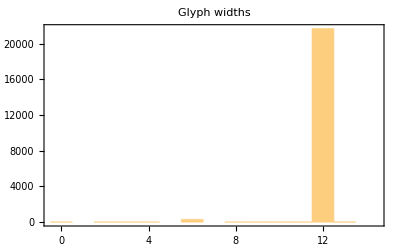

```mathematica
Print[Histogram[ToExpression/@widths,{-1/2,29/2,1},Frame->True,PlotRange->All,PlotLabel->"Glyph widths"]];
```

#### Indices of characters with widths ≠12

```mathematica
nonstdwidth=Flatten[Position[ToExpression/@widths,w_/;w≠12]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,100,101,104,105,106,107,108,109,110,113,114,115,117,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,325,326,329,332,333,336,339,345,346,347,349,350,351,352,353,354,355,356,357,358,359,360,361,362,364,365,366,369,370,372,373,374,375,376,387,388,403,404,405,407,412,416,418,419,420,437,441,442,451,452,667,668,1354,21834,21835,21836,21837,21838,21839,21840,21841,21842,21843,21855,21856,21857,21858,21859,21860,21861,21891,21974,21975,21976,21977,21978,21979,21980,21981,21982,21983,21984,21985,21986,21987,21988,21989,21990,21991,21992,21993,21994,21995,21996,21997,21998,21999,22000,22001,22002,22003,22004,22005,22006,22007,22008,22009,22010,22011,22012,22013,22014,22015,22016,22017,22018,22019,22020,22021,22022,22023,22024,22025,22026,22027,22028,22029,22030,22031,22032,22033,22034,22035,22036}

### Extract bounding box dimensions

```mathematica
Dimensions[boundingboxes=Flatten[Select[#,First[#]=="BBX"&]]&/@charlines]
```

{22043,5}

### Extract bounding box sizes

```mathematica
Dimensions[sizes=Take[#,{2,3}]&/@ToExpression[boundingboxes]]
```

{22043,2}

#### Maximum bounding box size

```mathematica
maxsize=MapThread[Apply,{{Max,Max},Transpose[sizes]}]
```

{12,12}

#### Bounding box size statistics

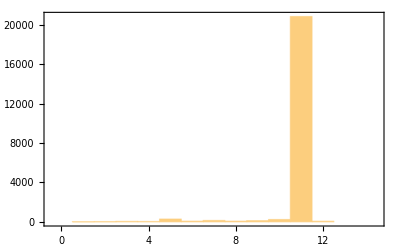

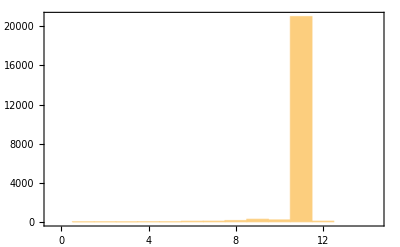

```mathematica
Print[Histogram[#,{-1/2,29/2,1},Frame->True,PlotRange->All]]&/@Transpose[sizes];
```

1
25 | 2
36 | 3
56 | 4
45 | 5
294 | 6
79 | 7
150 | 8
79 | 9
127 | 10
247 | 11
20832 | 12
73
1
27 | 2
28 | 3
23 | 4
35 | 5
31 | 6
76 | 7
84 | 8
147 | 9
281 | 10
212 | 11
21015 | 12
84

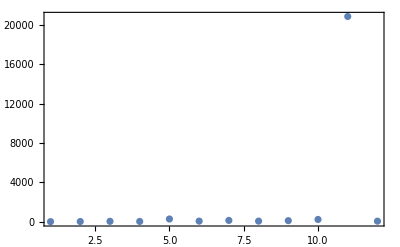

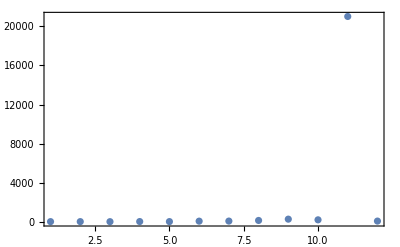

```mathematica
TableForm[Sort[Tally[#],#1⟦1⟧<#2⟦1⟧&]&/@Transpose[sizes]]
Print[ListPlot[#,Frame->True,PlotRange->All]]&/@%;
```

### Extract bounding box positions

```mathematica
bounds=Flatten[{Take[#,-2],Take[#,-2]+Take[#,{2,3}]}]&/@ToExpression[boundingboxes];
```

```mathematica
Dimensions[bounds]
```

{22043,4}

#### Envelope of all bounding boxes

```mathematica
bigbox=MapThread[Apply,{{Min,Min,Max,Max},Transpose[bounds]}]
```

{-5,-2,14,11}

#### Bounding box statistics

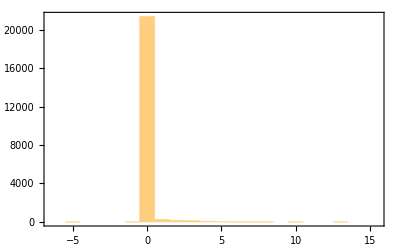

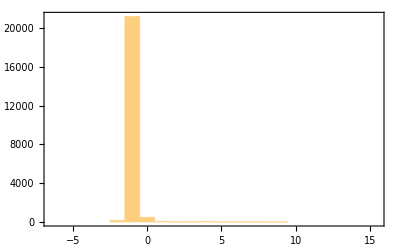

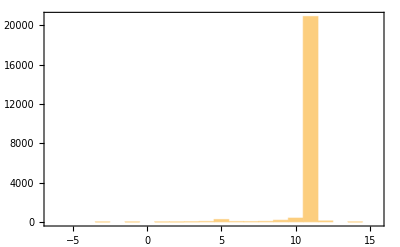

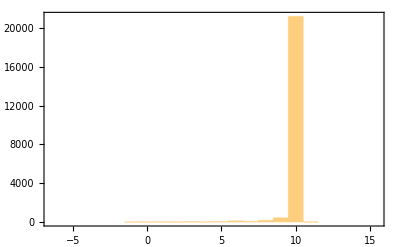

```mathematica
Print[Histogram[#,{-13/2,31/2,1},Frame->True,PlotRange->All]]&/@Transpose[bounds];
```

-5
2 | -1
1 | 0
21400 | 1
246 | 2
155 | 3
128 | 4
55 | 5
35 | 6
9 | 7
8 | 8
2 | 10
1 | 13
1 |  | 
-2
149 | -1
21225 | 0
475 | 1
54 | 2
20 | 3
26 | 4
47 | 5
6 | 6
15 | 7
13 | 8
10 | 9
3 |  |  | 
-3
1 | -1
1 | 1
3 | 2
4 | 3
24 | 4
50 | 5
247 | 6
43 | 7
38 | 8
56 | 9
174 | 10
395 | 11
20903 | 12
103 | 14
1
-1
3 | 0
3 | 1
7 | 2
4 | 3
13 | 4
5 | 5
41 | 6
102 | 7
56 | 8
155 | 9
419 | 10
21232 | 11
3 |  |

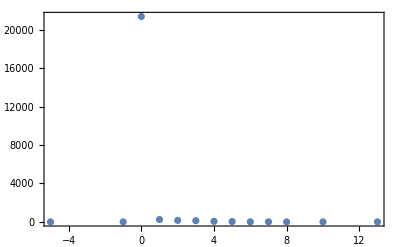

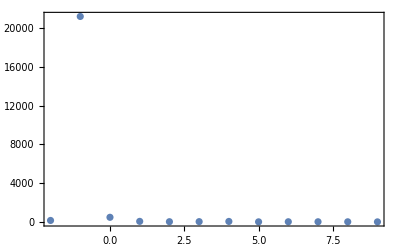

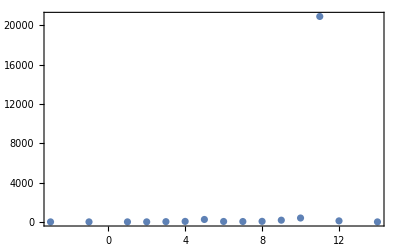

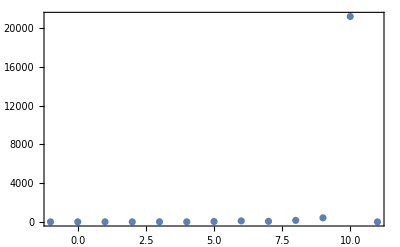

```mathematica
TableForm[Sort[Tally[#],#1⟦1⟧<#2⟦1⟧&]&/@Transpose[bounds]]
Print[ListPlot[#,Frame->True,PlotRange->All]]&/@%;
```

#### Indices of bounding box position outliers

```mathematica
outliers=Flatten[Position[bounds,{l_,b_,r_,t_}/;l<0||b<-1||r>11||t>11]]
```

{1,13,64,93,101,116,134,166,236,237,240,241,247,250,254,255,256,263,265,281,284,295,307,310,311,313,316,327,328,329,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,646,658,659,661,668,675,1033,2300,3362,5390,6077,6760,6787,8423,9419,13735,13789,14038,15261,15906,16400,17659,17900,20505,21427,21576,21590,21706,21829,21831,21840,21858,21877,21891,21942,21950,21953,21959,21960,21968,21971,22040}

### Extend glyph bitmaps to full font bounding box dimensions

```mathematica
fills=#-bigbox&/@bounds;
```

```mathematica
Take[fills,16]
```

{{18,0,0,-12},{7,2,-11,-2},{6,9,-10,-2},{5,2,-9,-2},{5,1,-9,-1},{5,2,-8,-3},{5,2,-9,-2},{7,9,-11,-2},{7,1,-9,-1},{6,1,-10,-1},{5,4,-9,-4},{5,4,-9,-4},{5,0,-12,-10},{5,6,-9,-6},{7,2,-11,-9},{6,2,-10,-2}}

```mathematica
Dimensions[bitmaps=Function[{line},
Block[{bounds=ToExpression[Drop[Flatten[Select[line,First[#]=="BBX"&]],1]]},
1-Take[HexExpand[#],bounds⟦1⟧]&/@Flatten[Take[line,{1,-1}+Flatten[Position[line,#]&/@{{"BITMAP"},{"ENDCHAR"}}]]]
]
]/@charlines]
```

{22043}

```mathematica
Take[bitmaps,16]
```

{{{1}},{{0},{0},{0},{0},{0},{0},{1},{0},{0}},{{0,1,0},{0,1,0}},{{1,0,1,0,1},{1,0,1,0,1},{0,0,0,0,0},{1,0,1,0,1},{1,0,1,0,1},{1,0,1,0,1},{0,0,0,0,0},{1,0,1,0,1},{1,0,1,0,1}},{{1,1,0,1,1},{1,0,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{1,0,0,1,1},{1,1,0,1,1},{1,1,0,0,1},{1,1,0,1,0},{0,1,0,1,0},{1,0,0,0,1},{1,1,0,1,1}},{{1,0,1,1,0,1},{0,1,0,1,0,1},{0,1,0,0,1,1},{1,0,1,0,1,1},{1,1,0,1,0,1},{1,1,0,0,1,0},{1,0,1,0,1,0},{1,0,1,1,0,1}},{{1,0,0,1,1},{0,1,1,0,1},{0,1,1,0,1},{1,0,0,1,1},{1,0,1,1,1},{0,1,0,1,0},{0,1,0,1,0},{0,1,1,0,1},{1,0,0,1,0}},{{0},{0}},{{1,1,0},{1,0,1},{1,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{1,0,1},{1,0,1},{1,1,0}},{{0,1,1},{1,0,1},{1,0,1},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{0,1,1}},{{1,1,0,1,1},{1,1,0,1,1},{0,0,0,0,0},{1,1,0,1,1},{1,0,1,0,1}},{{1,1,0,1,1},{1,1,0,1,1},{0,0,0,0,0},{1,1,0,1,1},{1,1,0,1,1}},{{1,0},{1,0},{0,1}},{{0,0,0,0,0}},{{0},{0}},{{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{1,0,1},{0,1,1},{0,1,1},{0,1,1}}}

```mathematica
BitmapExtend=Function[{bitmap,fill},
Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},
bmp=Join[xl,#,xr]&/@bitmap;
yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];
yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];
Join[yt,bmp,yb]
]
]
```

Function[{bitmap,fill},Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},bmp=(Join[xl,#1,xr]&)/@bitmap;yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];Join[yt,bmp,yb]]]

```mathematica
Dimensions[extbitmaps=MapThread[BitmapExtend,{bitmaps,fills}]]
```

{22043,13,19}

```mathematica
bigbox
```

{-5,-2,14,11}

### Truncate glyphs to 12×12 bitmap

```mathematica
BitmapTruncate=Function[bitmap,Take[#,{6,17}]&/@Take[bitmap,{2,13}]]
```

Function[bitmap,(Take[#1,{6,17}]&)/@Take[bitmap,{2,13}]]

```mathematica
Dimensions[trbitmaps=BitmapTruncate/@extbitmaps]
```

{22043,12,12}

## Display glyphs

### Non standard width glyphs

```mathematica
nonstdwidthgraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width:"<>ToString[#3])]&,#⟦nonstdwidth⟧&/@{extbitmaps,charcodes,widths}];
```

```mathematica
nonstdwidthtruncgraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width:"<>ToString[#3])]&,#⟦nonstdwidth⟧&/@{trbitmaps,charcodes,widths}];
```

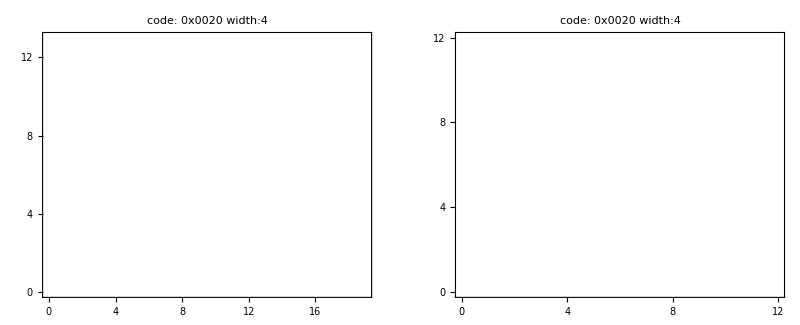

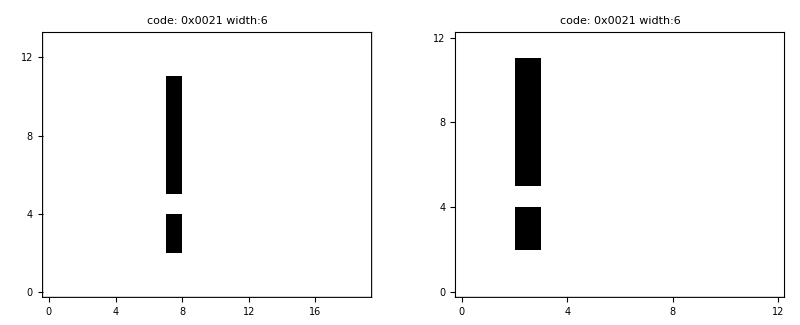

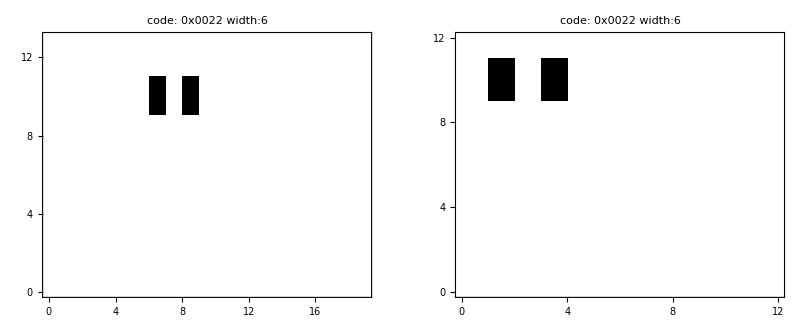

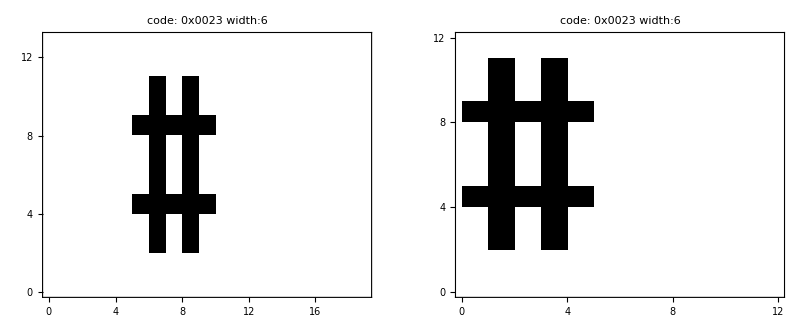

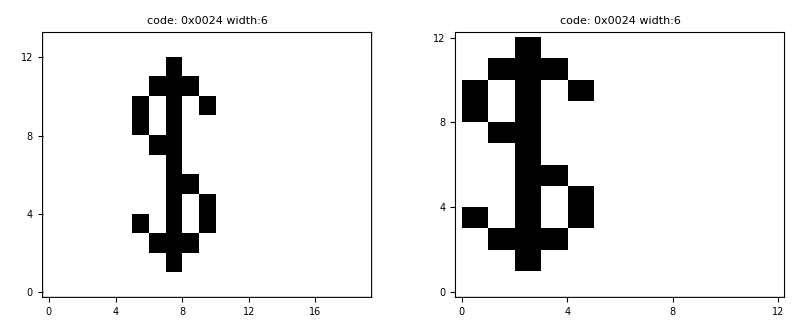

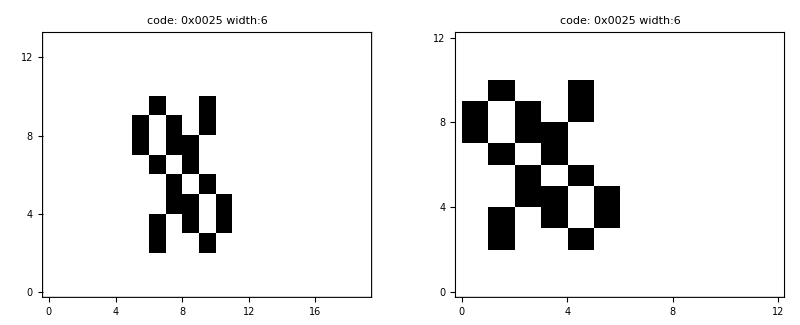

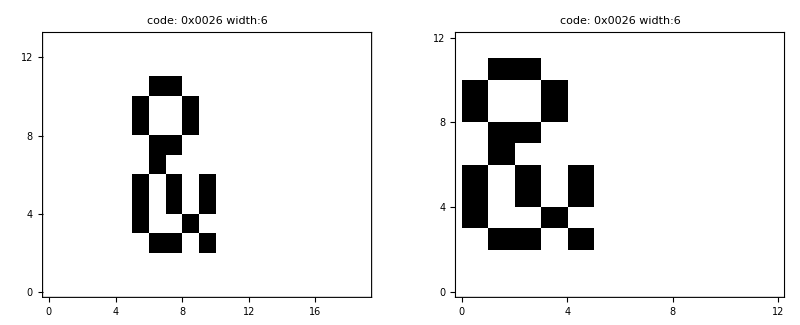

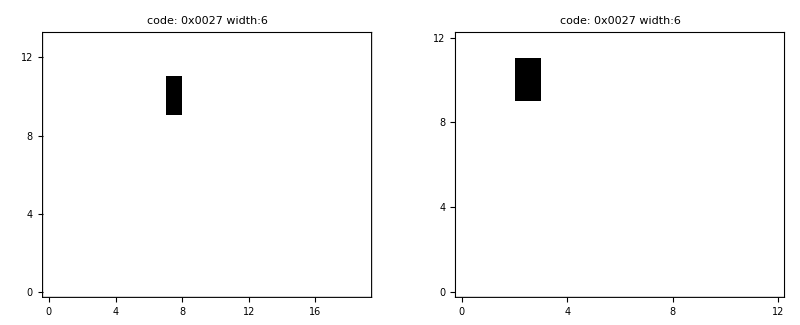

-Graphics-

-Graphics-

-Graphics-

«219 more identical outputs»

```mathematica
MapThread[Print[GraphicsGrid[{{##}}]]&,{nonstdwidthgraphics,nonstdwidthtruncgraphics}];
```

### Bounding box outlier glyphs

```mathematica
outliergraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width: "<>ToString[#3])]&,#⟦outliers⟧&/@{extbitmaps,charcodes,widths}];
```

```mathematica
outliertruncgraphics=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4])]&,#⟦outliers⟧&/@{trbitmaps,charcodes,widths}];
```

```mathematica
MapThread[Print[GraphicsGrid[{{##}}]]&,{outliergraphics,outliertruncgraphics}];
```

-Graphics-

-Graphics-

-Graphics-

«188 more identical outputs»

### All glyphs

```mathematica
bitmapgrafix=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width: "<>ToString[#3])]&,{extbitmaps,charcodes,widths}];
```

```mathematica
bitmaptrgrafix=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4]<>" width: "<>ToString[#3])]&,{trbitmaps,charcodes,widths}];
```

```mathematica
MapThread[Print[GraphicsGrid[{{##}}]]&,Take[#,1024]&/@{bitmapgrafix,bitmaptrgrafix}];
```

-Graphics-

-Graphics-

-Graphics-

«1021 more identical outputs»

## Extract and sort glyphs by Table of General Standard Chinese Characters

```mathematica
Take[rawunicodetable,16]
```

{{#,Table,of,General,Standard,Chinese,Characters,mapped,to,Unicode},{index,number,codepoint},{1,U+4E00},{2,U+4E59},{3,U+4E8C},{4,U+5341},{5,U+4E01},{6,U+5382},{7,U+4E03},{8,U+535C},{9,U+516B},{10,U+4EBA},{11,U+5165},{12,U+513F},{13,U+5315},{14,U+51E0}}

#### Check if the TGSCC is contiguous

```mathematica
{Max[#],Min[#]}&[ListConvolve[{1,-1},First/@Drop[rawunicodetable,2]]]
```

{1,1}

Yes, it is.

```mathematica
Take[TGSCCcodes=ToExpression[StringReplace[Last[#],"U+"->"16^^"]]&/@Drop[rawunicodetable,2],16]
```

{19968,20057,20108,21313,19969,21378,19971,21340,20843,20154,20837,20799,21269,20960,20061,20993}

```mathematica
Dimensions[lookuptable=Association[MapThread[Function[{code,trbitmap,extbitmap,width},ToExpression[code]->{trbitmap,extbitmap,width}],{charcodes,trbitmaps,extbitmaps,widths}]]]
```

{22043}

```mathematica
Graphics[Raster[Reverse[#1⟦2⟧]],Frame->True,AspectRatio->Divide@@Dimensions[#1⟦2⟧],PlotLabel->"Unicode:"<>IntegerString[#1⟦1⟧,16,4]<>" width:"<>ToString[#1⟦-1⟧],FrameTicks->({#,#,{},{}}&[Range[0,16,4]])]&/@Take[Prepend[Lookup[lookuptable,#],#]&/@TGSCCcodes,1500]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Export bitmaps into C files

### Build an extraction function, step by step

```mathematica
MatrixForm[#⟦51⟧]&/@{trbitmaps,charcodes,widths}
```

{(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1),82,6}

#### The sino:bit display is organized in columns, so transpose the 12 ×12 array

```mathematica
MatrixForm[1-Transpose[trbitmaps⟦51⟧]]
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### The columns get assembled into 12-bit words for starters

```mathematica
BaseForm[WordBuild/@(1-Transpose[trbitmaps⟦51⟧]),2]
%
```

{11111111100_2,10001000000_2,10001000000_2,10001100000_2,1110011100_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2}

{2044,1088,1088,1120,924,0,0,0,0,0,0,0}

#### For more efficient use of memory, the 12-bit words get split into 8+4 bits in two different arrays

```mathematica
BaseForm[Block[{t=(1-Transpose[trbitmaps⟦51⟧])},{WordBuild[Take[#,8]]&/@t,WordBuild[Take[#,-4]]&/@t}],2]
%
```

{{1111111_2,1000100_2,1000100_2,1000110_2,111001_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2},{1100_2,0_2,0_2,0_2,1100_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2}}

{{127,68,68,70,57,0,0,0,0,0,0,0},{12,0,0,0,12,0,0,0,0,0,0,0}}

#### The 4-bit array gets compressed into a byte array

```mathematica
BaseForm[Block[{t=(1-Transpose[trbitmaps⟦51⟧])},{WordBuild[Take[#,8]]&/@t,WordBuild/@Partition[Flatten[Take[#,-4]&/@t],8]}],2]
%
```

{{1111111_2,1000100_2,1000100_2,1000110_2,111001_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2},{11000000_2,0_2,11000000_2,0_2,0_2,0_2}}

{{127,68,68,70,57,0,0,0,0,0,0,0},{192,0,192,0,0,0}}

#### The arrays get concatenated; 12 × 12 bits get mapped into 12+12/2==18 bytes

```mathematica
BaseForm[Block[{t=(1-Transpose[trbitmaps⟦51⟧])},Flatten[{WordBuild[Take[#,8]]&/@t,WordBuild/@Partition[Flatten[Take[#,-4]&/@t],8]}]],2]
%
```

{1111111_2,1000100_2,1000100_2,1000110_2,111001_2,0_2,0_2,0_2,0_2,0_2,0_2,0_2,11000000_2,0_2,11000000_2,0_2,0_2,0_2}

{127,68,68,70,57,0,0,0,0,0,0,0,192,0,192,0,0,0}

#### Now we have a function

```mathematica
ht1632bitmap=Function[bitmap12x12,Block[{t=1-Transpose[bitmap12x12]},Flatten[{WordBuild[Take[#,8]]&/@t,WordBuild/@Partition[Flatten[Take[#,-4]&/@t],8]}]]]
```

Function[bitmap12x12,Block[{t=1-Transpose[bitmap12x12]},Flatten[{(WordBuild[Take[#1,8]]&)/@t,WordBuild/@Partition[Flatten[(Take[#1,-4]&)/@t],8]}]]]

```mathematica
ht1632bitmap[trbitmaps⟦51⟧]
```

{127,68,68,70,57,0,0,0,0,0,0,0,192,0,192,0,0,0}

### Export compressed glyph data

```mathematica
missingcode=Reverse[IntegerDigits[#,2,12]&/@{2^^111111111111,2^^111000000111,2^^110111111011,2^^101111111101,2^^101011110101,2^^101100001101,2^^101111111101,2^^101111111101,2^^101101101101,2^^110111111011,2^^111000000111,2^^111111111111}]
```

{{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,0,0,0,0,0,0,1,1,1},{1,1,0,1,1,1,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,1,1,0,1},{1,0,1,1,1,1,1,1,1,1,0,1},{1,0,1,1,1,1,1,1,1,1,0,1},{1,0,1,1,0,0,0,0,1,1,0,1},{1,0,1,0,1,1,1,1,0,1,0,1},{1,0,1,1,1,1,1,1,1,1,0,1},{1,1,0,1,1,1,1,1,1,0,1,1},{1,1,1,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
glyphstatement=Function[{vartype,varname,bitmaps},vartype<>" "<>varname<>"[][18]= {\n    "
<>StringRiffle[ToString[ht1632bitmap[#]]&/@bitmaps,",\n    "]<>"\n};\n"]
```

Function[{vartype,varname,bitmaps},vartype<> <>varname<>[][18]= {
    <>StringRiffle[(ToString[ht1632bitmap[#1]]&)/@bitmaps,,
    ]<>
};
]

```mathematica
glyphstatement["const uint8_t","glyph",{missingcode}]
```

const uint8_t glyph[][18]= {
    {0, 31, 32, 65, 82, 66, 66, 82, 65, 32, 31, 0, 8, 66, 34, 34, 36, 128}
};

```mathematica
glyphstatement["const uint8_t","glyph",Take[Lookup[lookuptable,#,{missingcode,{},12}]⟦1⟧&/@TGSCCcodes,32]]
```

const uint8_t glyph[][18]= {
    {8, 8, 8, 8, 8, 8, 8, 8, 8, 8, 8, 0, 0, 0, 0, 0, 0, 0},
    {128, 129, 130, 132, 136, 144, 160, 192, 192, 128, 1, 0, 194, 34, 34, 34, 34, 192},
    {0, 64, 64, 64, 64, 64, 64, 64, 64, 64, 0, 0, 68, 68, 68, 68, 68, 64},
    {4, 4, 4, 4, 4, 255, 4, 4, 4, 4, 4, 0, 0, 0, 14, 0, 0, 0},
    {128, 128, 128, 128, 128, 255, 128, 128, 128, 128, 128, 0, 0, 2, 46, 0, 0, 0},
    {0, 255, 128, 128, 128, 128, 128, 128, 128, 128, 128, 0, 104, 0, 0, 0, 0, 0},
    {8, 8, 255, 8, 16, 16, 16, 16, 32, 32, 32, 0, 0, 226, 34, 34, 34, 224},
    {0, 0, 0, 0, 255, 16, 16, 8, 8, 4, 2, 0, 0, 0, 224, 0, 0, 0},
    {0, 0, 7, 248, 0, 0, 0, 248, 7, 0, 0, 0, 44, 0, 0, 0, 12, 32},
    {0, 0, 0, 3, 12, 240, 12, 3, 0, 0, 0, 0, 36, 128, 0, 0, 132, 32},
    {0, 0, 128, 131, 140, 240, 12, 3, 0, 0, 0, 0, 36, 128, 0, 0, 132, 32},
    {0, 0, 0, 255, 0, 0, 0, 255, 0, 0, 1, 0, 34, 192, 0, 14, 34, 224},
    {255, 4, 4, 4, 8, 8, 8, 16, 16, 33, 0, 0, 226, 34, 34, 34, 46, 0},
    {0, 0, 1, 254, 128, 128, 128, 255, 0, 0, 1, 0, 36, 128, 0, 14, 34, 224},
    {32, 32, 33, 254, 32, 32, 32, 63, 0, 0, 3, 0, 36, 128, 0, 14, 34, 224},
    {129, 129, 129, 130, 130, 132, 132, 136, 136, 128, 255, 0, 0, 0, 0, 2, 34, 224},
    {128, 128, 128, 128, 128, 135, 136, 144, 160, 192, 0, 0, 0, 2, 46, 0, 0, 0},
    {128, 128, 129, 134, 248, 128, 128, 128, 128, 128, 255, 0, 36, 128, 0, 2, 34, 224},
    {32, 32, 32, 35, 252, 32, 32, 32, 32, 32, 63, 0, 36, 128, 0, 2, 34, 224},
    {128, 128, 135, 248, 128, 128, 128, 152, 232, 136, 15, 0, 44, 0, 0, 2, 34, 224},
    {128, 176, 136, 132, 130, 129, 130, 132, 152, 224, 0, 0, 34, 68, 128, 132, 66, 32},
    {64, 68, 68, 68, 68, 68, 68, 68, 68, 68, 64, 0, 34, 34, 34, 34, 34, 32},
    {4, 132, 132, 132, 132, 255, 132, 132, 132, 132, 4, 0, 0, 0, 14, 0, 0, 0},
    {4, 132, 132, 132, 132, 255, 132, 132, 132, 132, 4, 0, 0, 2, 46, 0, 0, 0},
    {16, 18, 150, 154, 146, 146, 146, 146, 146, 19, 16, 0, 0, 4, 66, 36, 128, 0},
    {128, 128, 128, 128, 128, 255, 128, 128, 128, 128, 128, 0, 34, 34, 46, 34, 34, 32},
    {0, 8, 8, 8, 8, 255, 8, 8, 8, 8, 0, 0, 34, 34, 46, 34, 34, 32},
    {16, 16, 16, 16, 16, 255, 16, 16, 16, 16, 16, 0, 2, 34, 46, 34, 34, 0},
    {32, 32, 32, 33, 33, 34, 255, 36, 40, 32, 32, 0, 136, 128, 34, 224, 0, 0},
    {128, 128, 128, 128, 255, 128, 144, 136, 132, 130, 128, 0, 0, 0, 224, 0, 0, 0},
    {32, 32, 36, 35, 32, 32, 32, 255, 32, 32, 32, 0, 0, 0, 2, 46, 0, 0},
    {32, 32, 32, 35, 44, 240, 44, 35, 32, 32, 32, 0, 36, 128, 0, 0, 132, 32}
};

### Export character codes

```mathematica
codestatement=Function[{vartype,varname,codes},vartype<>" "<>varname<>"[][3]= {\n    {0x"
<>StringRiffle[StringRiffle[StringPartition[IntegerString[ToExpression[#],16,6],2],", 0x"]&/@codes,"},\n    {0x"]<>"}\n};\n"]
```

Function[{vartype,varname,codes},vartype<> <>varname<>[][3]= {
    {0x<>StringRiffle[(StringRiffle[StringPartition[IntegerString[ToExpression[#1],16,6],2],, 0x]&)/@codes,},
    {0x]<>}
};
]

```mathematica
codestatement["const uint8_t","codes",Take[TGSCCcodes,32]]
```

const uint8_t codes[][3]= {
    {0x00, 0x4e, 0x00},
    {0x00, 0x4e, 0x59},
    {0x00, 0x4e, 0x8c},
    {0x00, 0x53, 0x41},
    {0x00, 0x4e, 0x01},
    {0x00, 0x53, 0x82},
    {0x00, 0x4e, 0x03},
    {0x00, 0x53, 0x5c},
    {0x00, 0x51, 0x6b},
    {0x00, 0x4e, 0xba},
    {0x00, 0x51, 0x65},
    {0x00, 0x51, 0x3f},
    {0x00, 0x53, 0x15},
    {0x00, 0x51, 0xe0},
    {0x00, 0x4e, 0x5d},
    {0x00, 0x52, 0x01},
    {0x00, 0x4e, 0x86},
    {0x00, 0x52, 0x00},
    {0x00, 0x52, 0x9b},
    {0x00, 0x4e, 0x43},
    {0x00, 0x53, 0xc8},
    {0x00, 0x4e, 0x09},
    {0x00, 0x5e, 0x72},
    {0x00, 0x4e, 0x8e},
    {0x00, 0x4e, 0x8f},
    {0x00, 0x5d, 0xe5},
    {0x00, 0x57, 0x1f},
    {0x00, 0x58, 0xeb},
    {0x00, 0x62, 0x4d},
    {0x00, 0x4e, 0x0b},
    {0x00, 0x5b, 0xf8},
    {0x00, 0x59, 0x27}
};

### Export the files

```mathematica
Export["charcode.c.snippet",codestatement["const uint16_t","charcode",TGSCCcodes],"String"]
```

charcode.c.snippet

```mathematica
Export["glyph.c.snippet",glyphstatement["const uint8_t","glyph",Lookup[lookuptable,#,{missingcode,{},12}]⟦1⟧&/@TGSCCcodes],"String"]
```

glyph.c.snippet